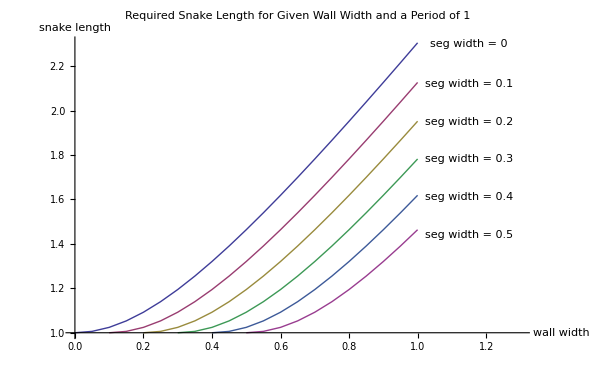

```mathematica
(*
P = 1;
A = 1;
l = 0.15;
w = 0.1;
*)

getLimits[P_,A_,l_,segWidth_]:=Module[{expr1, expr2, subs1, subs2, sol, xrule1, xrule2, xval1, xval2, yrule1, yrule2, yval1, yval2, angle, y, x},
Off[Reduce::ratnz];
Off[Reduce::incs];
expr1 = l^2 == (x-P/2)^2 + (y+A/2)^2;expr2 = y == A/2 * Cos[2*Pi*x/P];
subs1  = Solve[expr1, {y}];
subs2  = Solve[expr2, {y}]; sol =Reduce[expr1 && expr2  && x > 0 && x < P, {x,y}, Reals];xrule1=Solve[sol[[1]][[1]],x];
xrule2=Solve[sol[[2]][[1]],x];
xval1 =(x /. xrule1) [[1]];
xval2 =(x /. xrule2 )[[1]] ;yrule1 =Solve[sol[[1]][[2]] /. xrule1[[1]],y];yrule2 =Solve[sol[[2]][[2]] /. xrule2[[1]],y];yval1 =(y /. yrule1) [[1]];
yval2 =(y /. yrule2 )[[1]] ;
angle = ArcSin[(yval1+A/2)/l];
segWidth/2 * Cos[angle]]


getLength[P_,W_] := Module[{L}, 2*(P^2/4 + W^2)^(1/2)]

getLengthAnchor[P_, W_, segWidth_] := Module[{x},
Integrate[(((-(W-segWidth)Pi/P )*Sin[2Pi*x/P])^2+1)^(1/2),{ x, 0, P}]
]

results = {{{0.,1.},{0.05,1.0061402544253308},{0.1,1.024235228564182},{0.15000000000000002,1.0533960261691375},{0.2,1.0923835473311778},{0.25,1.1398386643694227},{0.30000000000000004,1.1944523009924373},{0.35000000000000003,1.255057045703324},{0.4,1.320658226693122},{0.45,1.3904299495666794},{0.5,1.4636954724135356},{0.55,1.5399031882599155},{0.6000000000000001,1.6186036276736517},{0.65,1.6994295473738867},{0.7000000000000001,1.782079525980375},{0.75,1.8663047918006948},{0.8,1.95189878007281},{0.8500000000000001,2.038688897811047},{0.9,2.1265300347065237},{0.9500000000000001,2.2152994397675827},{1.,2.3048926613536915}},{{0.1,1.},{0.15000000000000002,1.0061402544253308},{0.2,1.024235228564182},{0.25,1.0533960261691369},{0.30000000000000004,1.0923835473311778},{0.35000000000000003,1.1398386643694227},{0.4,1.1944523009924373},{0.45,1.255057045703324},{0.5,1.320658226693122},{0.55,1.3904299495666794},{0.6000000000000001,1.4636954724135363},{0.65,1.5399031882599155},{0.7000000000000001,1.6186036276736517},{0.75,1.6994295473738867},{0.8,1.782079525980375},{0.8500000000000001,1.8663047918006945},{0.9,1.95189878007281},{0.9500000000000001,2.038688897811047},{1.,2.1265300347065237}},{{0.2,1.},{0.25,1.0061402544253308},{0.30000000000000004,1.024235228564182},{0.35000000000000003,1.0533960261691375},{0.4,1.0923835473311778},{0.45,1.1398386643694227},{0.5,1.1944523009924373},{0.55,1.255057045703324},{0.6000000000000001,1.320658226693122},{0.65,1.3904299495666794},{0.7000000000000001,1.4636954724135356},{0.75,1.5399031882599155},{0.8,1.6186036276736517},{0.8500000000000001,1.6994295473738865},{0.9,1.7820795259803746},{0.9500000000000001,1.8663047918006948},{1.,1.95189878007281}},{{0.30000000000000004,1.},{0.35000000000000003,1.0061402544253308},{0.4,1.024235228564182},{0.45000000000000007,1.0533960261691375},{0.5,1.0923835473311776},{0.55,1.1398386643694227},{0.6000000000000001,1.1944523009924373},{0.65,1.255057045703324},{0.7000000000000001,1.320658226693122},{0.7500000000000001,1.3904299495666794},{0.8,1.4636954724135356},{0.8500000000000001,1.5399031882599155},{0.9000000000000001,1.6186036276736517},{0.9500000000000001,1.6994295473738867},{1.,1.7820795259803746}},{{0.4,1.},{0.45,1.0061402544253308},{0.5,1.024235228564182},{0.55,1.0533960261691375},{0.6000000000000001,1.0923835473311778},{0.65,1.1398386643694227},{0.7000000000000001,1.1944523009924373},{0.75,1.255057045703324},{0.8,1.320658226693122},{0.8500000000000001,1.3904299495666794},{0.9,1.4636954724135356},{0.9500000000000001,1.5399031882599155},{1.,1.6186036276736517}},{{0.5,1.},{0.55,1.0061402544253308},{0.6,1.024235228564182},{0.65,1.0533960261691375},{0.7,1.0923835473311776},{0.75,1.1398386643694227},{0.8,1.1944523009924373},{0.85,1.255057045703324},{0.9,1.320658226693122},{0.9500000000000001,1.3904299495666794},{1.,1.4636954724135356}}};

graphResult = ListLinePlot[results,PlotLabel->Style["Required Snake Length for Given Wall Width and a Period of 1",20], AxesLabel->{Style["wall width",15],Style["snake length",15]},
PlotRange->{{0,1.3},Automatic},
ImageSize->600,
Epilog->{Style[Text["seg width = 0",{1.15,2.3}],15],
Style[Text["seg width = 0.1",{1.15,2.12}],15],
Style[Text["seg width = 0.2",{1.15,1.95}],15],
Style[Text["seg width = 0.3",{1.15,1.78}],15],
Style[Text["seg width = 0.4",{1.15,1.61}],15],
Style[Text["seg width = 0.5",{1.15,1.44}],15]

}]

(*
expr = getLengthAnchor[1,Z,V]
results = Table[{Z, expr} ,{V,0, 0.5, 0.1}, {Z, V,1, 0.05}]
graphResult = ListLinePlot[results,PlotLabel->Style["Required Snake Length for Given Wall Width",20], AxesLabel->{Style["wall width",15],Style["snake length",15]},
PlotRange->{{0,1.3},Automatic},
ImageSize->600,
Epilog->{Style[Text["seg width = 0",{1.15,2.3}],15],
Style[Text["seg width = 0.1",{1.15,2.12}],15],
Style[Text["seg width = 0.2",{1.15,1.95}],15],
Style[Text["seg width = 0.3",{1.15,1.78}],15],
Style[Text["seg width = 0.4",{1.15,1.61}],15],
Style[Text["seg width = 0.5",{1.15,1.44}],15]

}]
*)
(*
expr = getLengthAnchor[1,W,w]
results = Table[{W, expr} /. {w->V , W->Z},{V,0, 0.5, 0.1}, {Z, V,1, 0.05}]
graphResult = ListLinePlot[results,PlotLabel->Style["Required Snake Length for Given Wall Width",20], AxesLabel->{Style["wall width",15],Style["snake length",15]},
PlotRange->{{0,1.3},Automatic},
ImageSize->600,
Epilog->{Style[Text["seg width = 0",{1.15,2.3}],15],
Style[Text["seg width = 0.1",{1.15,2.12}],15],
Style[Text["seg width = 0.2",{1.15,1.95}],15],
Style[Text["seg width = 0.3",{1.15,1.78}],15],
Style[Text["seg width = 0.4",{1.15,1.61}],15],
Style[Text["seg width = 0.5",{1.15,1.44}],15]

}]
*)


(*
expr = getLengthAnchor[1,W,w]
expr = Hold[expr]

results = Table[Hold[expr]  /. {w->V , W->Z},{V,0, 0.5, 0.05}, {Z, 0,2, 0.05}]
Plot[ReleaseHold[results], {W, 0, 2}]
*)
(*
expr = Hold[getLengthAnchor[1,W,w]]
results = Table[expr  /. w->V ,{V,0, 0.5, 0.05}]

Plot[ReleaseHold[results], {W, 0, 2}]
*)
(*
expr = Hold[{y, getLengthAnchor[1,y,0]}]
results = Table[expr /. y ->  x, {x,0, 2, 0.05}];
results2 = ReleaseHold[results]
graphResult = ListLinePlot[results2]
*)
(*
expr = getLength[1,x]
Plot[expr, {x,0,2}]
*)

(*
getLimits[1,1,0.15,0.1];
getLimits[1,1,0.15,0.15];

expr = getLimits[1,1,0.15,x];
Plot[expr, {x,0.0,1.0}];

expr = Hold[{y, getLimits[1,1,y,0.1]}];

results = Table[expr /. y ->  x, {x,0.05, 1.05, 0.05}];
results2 = ReleaseHold[results];

graphResult = ListLinePlot[results2];
graphResult
*)

(* vals  = Range[0.01, 0.02, 0.001] *)

(* expr = getLimits[1,1,vals,0.1] *)

(* Plot[expr, {x,0.01,0.02}] *)




(* Plot[{y /. subs2, y /. subs1[[2]], y /. subs1[[1]]}, {x,0,P}] *)



(* x values in rule form *)





(* y values in rule form *)





(* angle = ArcCos[(xval2-P/2)/l]; *)

(* If[xval1 > xval2, v = 1, v =0] *)

(* lower and upper limit of distance from curve to the wall with a given robot configuration of l, w, and curve paramters of A and P *)
```